# R0 on a landscape

We want to show how the landscape-level R0 value can affect things like time to extinction, but also look at how a theoretically calculated vs a simulated R0 value compare. 

What this will look like is: 
- Setting up some simulations to look at how changing R0 will change the results. Goal here is to:
	1. Loop over R0 ∈ {0.8,1.0,…,2.6}
	2. For each R0​, compute:
		-extinction time per run
		-mean & variance of infected counts over time
		-max proportion infected
		-epidemic size
		-duration above threshold (e.g. It>10It​>10)
	3. Aggregate summary statistics across 1000 simulations

## R0 changing persistence of pathogen

```mathematica
(* 1. PARAMETERS AND SETUP --------------------------------------------------- *)

ClearAll["Global`*"]
SeedRandom[123]; (* set seed so stuff is reproducible *)
(*First, some directory stuff for outputting plot*)
baseDir="/Users/colebrookson/github/theRmal-landscape/";
figsDir = FileNameJoin[{NotebookDirectory[], "..", "..", "figs", "si", "r0-simulations"}];
relativePath[parts__]:=FileNameJoin[{baseDir,parts}];

numPatches = 200000; (* number of spatial patches *)
initialInfected = 1; (* start with just one infected person *)
r0Values = Range[0.8, 2.6, 0.2]; (* range of quasi-r0 values *)
numReps = 100; (* how many runs to average over *)
maxTime = 100; (* max timesteps per run *)
threshold = 100000; (* for tracking how long the outbreak stays "big" *)
weights = ConstantArray[1/numPatches, numPatches]; (* uniform patch weight *)

(* 2. FUNCTION TO RUN ONE SIMULATION ----------------------------------------- *)

simulateRun[totalIndividuals_] := Module[
  {
    t = 0, NI = initialInfected, NT = totalIndividuals,
    infectedHistory = {}, Sloc, Iloc, cloc
  },

  (* while there's still infecteds and we haven't hit time limit *)
  While[NI > 0 && t < maxTime,
  
    (* randomly assign susceptibles and infecteds to patches *)
    Sloc = RandomChoice[weights -> Range[1, numPatches], NT - NI];
    Iloc = RandomChoice[weights -> Range[1, numPatches], NI];

    (* get list of patch IDs that have both S and I *)
    cloc = Intersection[Sloc, Iloc];

    (* count how many susceptibles were in those shared patches = new infecteds *)
    NI = Total[Count[Sloc, #] & /@ cloc];

    (* store current number of infecteds *)
    infectedHistory = Append[infectedHistory, NI];
    t++
  ];

  (* return summary stats for the run *)
  <|
    "ExtinctionTime" -> t,
    "InfectedTimeSeries" -> infectedHistory,
    "MaxProportionInfected" -> Max[infectedHistory]/totalIndividuals,
    "EpidemicSize" -> Total[infectedHistory],
    "DurationAboveThreshold" -> Count[infectedHistory, x_ /; x > threshold]
  |>
]

(* 2.1 FASTER FUNCTION MAYBE ------------------------------------------------- *)
ClearAll[simulateRunSparse]

simulateRunSparse[totalIndividuals_] := Module[
  {
    t = 0,
    IT = initialInfected,         (* current infecteds *)
    NT = totalIndividuals,        (* total population *)
    history = {},                 (* time-series record *)
    occ, patchSample, numInfPatches, sus, p, newInf,
    P = numPatches
  },

  occ = SparseArray[{}, {P}];     (* initialise empty occupancy vector *)

  While[IT > 0 && t < maxTime,

    (* 1 — drop infecteds on patches (sparse update) *)
    patchSample = RandomInteger[{1, P}, IT];
    occ += SparseArray[Normal[Counts[patchSample]], {P}];

    (* 2 — how many patches now have ≥1 infected? *)
    numInfPatches = Length@occ["NonzeroPositions"];

    (* 3 — draw new infections among susceptibles             *)
    sus = NT - IT;                (* susceptibles this step   *)
    p   = N[numInfPatches]/P;     (* share-a-patch probability*)
    newInf = If[sus <= 0,
                0,
                RandomVariate[BinomialDistribution[sus, p]]
              ];

    (* 4 — book-keeping *)
    AppendTo[history, IT];
    IT  = newInf;
    occ = SparseArray[{}, {P}];   (* infecteds die after one step *)
    t++
  ];

  <|
    "ExtinctionTime"         -> t,
    "InfectedTimeSeries"     -> history,
    "MaxProportionInfected"  -> Max[history]/totalIndividuals,
    "EpidemicSize"           -> Total[history],
    "DurationAboveThreshold" -> Count[history, x_ /; x > threshold]
  |>
]
```

### Run the simulations if needed or READ THEM FROM A FILE below this chunk

```mathematica
(* -------------------------------------------------------------- *)
(* 1 — ensure the parallel pool is up; count how many kernels     *)
LaunchKernels[];
numCores = $KernelCount;   (* how many kernels ParallelTable can use *)

(* -------------------------------------------------------------- *)
(* 2 — run the simulation block and time it                       *)
start  = AbsoluteTime[];

simulationResults = Association[];

Do[
  Module[
    {
      Nt = Round[r0*numPatches + initialInfected],
      counter = 0, results, extinctionTimes, timeSeriesList,
      propMax, sizes, durations, aligned, meanOverTime, varOverTime, maxLen
    },
    
    Print["Running simulations for R₀ = ", r0, " (Nt = ", Nt, ") …"];
    SetSharedVariable[counter];
    
    results = Monitor[
      ParallelTable[
        Module[{out = simulateRunSparse[Nt]},
          counter++; out],
        {numReps}
      ],
      Row[{
        "Progress: ", counter, "/", numReps, " (",
        Round[100.0*counter/numReps], "%)"
      }]
    ];
    
    (* ---- unpack and store results ---- *)
    extinctionTimes  = results[[All, "ExtinctionTime"]];
    timeSeriesList   = results[[All, "InfectedTimeSeries"]];
    propMax          = results[[All, "MaxProportionInfected"]];
    sizes            = results[[All, "EpidemicSize"]];
    durations        = results[[All, "DurationAboveThreshold"]];
    
    maxLen  = Min[maxTime, Max[Length /@ timeSeriesList]];
    aligned = Transpose[PadRight[#, maxLen, 0] & /@ timeSeriesList];
    
    meanOverTime = Mean /@ aligned;
    varOverTime  = Variance /@ aligned;
    
    simulationResults[r0] = <|
      "ExtinctionTimes"          -> extinctionTimes,
      "MeanInfectedOverTime"     -> meanOverTime,
      "InfectedTimeSeries"       -> timeSeriesList,
      "VarianceInfectedOverTime" -> varOverTime,
      "MaxProportionInfected"    -> propMax,
      "EpidemicSizes"            -> sizes,
      "DurationsAboveThreshold"  -> durations,
      "ExtinctionProbability"    -> Count[extinctionTimes, t_ /; t < maxTime]/numReps
    |>;
  ],
  {r0, r0Values}
];

elapsed = AbsoluteTime[] - start;   (* seconds *)

(* -------------------------------------------------------------- *)
(* 3 — human-readable summary                                     *)
Print[
  Row[{
    "Finished in ", NumberForm[elapsed, {8, 2}], " s  |  ",
    "numReps = ", numReps, ",  maxTime = ", maxTime, 
    ",  numPatches = ", numPatches, "  |  ",
    "parallel kernels = ", numCores
  }]
];

(* -------------------------------------------------------------- *)
(* 4 — export results                          *)
Export[
  FileNameJoin[{NotebookDirectory[], "..", "..", "outputs", 
                "intermediate-obs", "simResults.wl"}],
  simulationResults
]
```

LaunchKernels::nodef: Some parallel subkernels are already running. Not launching default kernels again.

Running simulations for R₀ = 0.8 (Nt = 160001) …

Running simulations for R₀ = 1. (Nt = 200001) …

Running simulations for R₀ = 1.2 (Nt = 240001) …

Running simulations for R₀ = 1.4 (Nt = 280001) …

Running simulations for R₀ = 1.6 (Nt = 320001) …

Running simulations for R₀ = 1.8 (Nt = 360001) …

Running simulations for R₀ = 2. (Nt = 400001) …

Running simulations for R₀ = 2.2 (Nt = 440001) …

Running simulations for R₀ = 2.4 (Nt = 480001) …

Running simulations for R₀ = 2.6 (Nt = 520001) …

Finished in 392.06 s  |  numReps = 100,  maxTime = 100,  numPatches = 200000  |  parallel kernels = 12

/Users/colebrookson/github/theRmal-landscape/src/mathematica/../../outputs/intermediate-obs/simResults.wl

```mathematica
(* read in instead of re-running *)
If[
  !ValueQ[simulationResults], 
  simulationResults = Import[
    FileNameJoin[
      {NotebookDirectory[], "..", "..", "outputs", "intermediate-obs", "simResults.wl"}
    ]
  ]
]
```

#### Let’s get a summary table so we can see roughly what the results say:

```mathematica
CI95[data_] := Quantile[data, {0.025, 0.975}];

summarizeR0[r_] := Module[
  {
    ext = simulationResults[r]["ExtinctionTimes"],
    epi = simulationResults[r]["EpidemicSizes"],
    dur = simulationResults[r]["DurationsAboveThreshold"],
    extCI, epiCI, durCI, varExt, varEpi, varDur
  },
  
  extCI = CI95[ext];
  epiCI = CI95[epi];
  durCI = CI95[dur];
  varExt = Variance[ext];
  varEpi = Variance[epi];
  varDur = Variance[dur];
  
  With[{round = Round[#, 0.01] &},  (* round to 2 decimal places *)
    {
      r,
      round@Mean[ext], round@extCI[[1]], round@extCI[[2]],
      round@Mean[epi], round@epiCI[[1]], round@epiCI[[2]],
      round@Mean[dur], round@durCI[[1]], round@durCI[[2]],
      round@varExt, round@varEpi, round@varDur
    }
  ]
];

summaryData = Prepend[
  summarizeR0 /@ r0Values,
  {
    "R₀",
    "Mean time to I=0", "I=0 CI Low", "I=0 CI High",
    "Mean Size", "CI Low", "CI High",
    "Mean Duration", "CI Low", "CI High", 
    "Var Time", "Var Size", "Var Duration"
  }
];
Grid[
  summaryData,
  Frame -> All,
  Alignment -> Center,
  Background -> {None, {LightGray, {}}},
  ItemStyle -> Directive[FontFamily -> "Helvetica", 12]
]
```

R₀ | Mean time to I=0 | I=0 CI Low | I=0 CI High | Mean Size | CI Low | CI High | Mean Duration | CI Low | CI High | Var Time | Var Size | Var Duration
0.8 | 2.79 | 1. | 12. | 5.9 | 1. | 29. | 0. | 0. | 0. | 10.29 | 334.66 | 0.
1. | 7.98 | 1. | 100. | 122.46 | 1. | 1198. | 0. | 0. | 0. | 324.77 | 487623. | 0.
1.2 | 26.06 | 1. | 100. | 298284. | 1. | 1.42342×10^6 | 0. | 0. | 0. | 1748.91 | 2.94912×10^11 | 0.
1.4 | 47.38 | 1. | 100. | 1.64047×10^6 | 1. | 3.82122×10^6 | 0. | 0. | 0. | 2387.33 | 3.20474×10^12 | 0.
1.6 | 72.48 | 1. | 100. | 4.29289×10^6 | 1. | 6.20574×10^6 | 0. | 0. | 0. | 1967.61 | 7.26058×10^12 | 0.
1.8 | 75.35 | 1. | 100. | 6.25262×10^6 | 1. | 8.57065×10^6 | 57.29 | 0. | 79. | 1841.36 | 1.31865×10^13 | 1107.48
2. | 77.4 | 1. | 100. | 8.21407×10^6 | 1. | 1.0924×10^7 | 62.63 | 0. | 83. | 1727.41 | 2.03801×10^13 | 1184.94
2.2 | 90.1 | 1. | 100. | 1.16723×10^7 | 1. | 1.32266×10^7 | 75.31 | 0. | 85. | 891. | 1.53252×10^13 | 638.16
2.4 | 88.17 | 1. | 100. | 1.34698×10^7 | 1. | 1.5572×10^7 | 75.35 | 0. | 87. | 1036.73 | 2.50237×10^13 | 783.22
2.6 | 87.14 | 1. | 100. | 1.53686×10^7 | 1. | 1.78984×10^7 | 75.81 | 0. | 88. | 1117.96 | 3.56711×10^13 | 868.05

### Plotting the results from the simulations:

#### We want plots that show: 1) the distribution of proportions of time to I = 0 for each value of R0

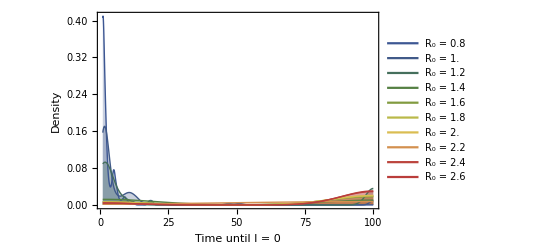

```mathematica
(* === Per-R0 filled KDEs of extinction times ============================== *)
(* 1) order keys and extract data *)
r0s = SortBy[Keys@simulationResults, N];            (* numeric order *)

extPerR0 = (simulationResults /@ r0s)[[All, "ExtinctionTimes"]];
(*list of sub-associations use Part [[All, "ExtinctionTimes"]]  *)

dataByR0 = AssociationThread[r0s, extPerR0];

(* optional: drop empty/non-numeric groups *)
dataByR0 = Select[dataByR0, VectorQ[#, NumericQ] && Length[#] > 0 &];

(* 2) one KDE per group; set bandwidth as you like *)
bw    = Automatic;             (* e.g., 0.6 or "Scott" also work *)
dists = Map[SmoothKernelDistribution[#, bw] &, dataByR0];

(* 3) common x-range (robust) *)
qMinMax = Map[Quantile[#, {0.01, 0.99}] &, Values@dataByR0];
{xMin, xMax} = {Max[0, Min@qMinMax[[All, 1]]], Max@qMinMax[[All, 2]]};

(* 4) colors/labels *)
n      = Length@dataByR0;
keys   = Keys@dataByR0; (* same order as r0s *)
colors = ColorData["DarkRainbow"] /@ Rescale[Range@n];
labels = Row[{"R₀ = ", #}] & /@ keys;

(* 5) plot per-curve filled KDEs with matching fills *)
Plot[
  Evaluate@Table[PDF[dists[r0], x], {r0, keys}],
  {x, xMin, xMax},
  Frame       -> True,
  FrameLabel  -> {"Time until I = 0", "Density"},
  PlotRange   -> All,
  PlotStyle   -> (Directive[#, Thick] & /@ colors),
  Filling     -> Axis,
  FillingStyle ->
    Thread[Range@n -> (Directive[#, Opacity[.28]] & /@ colors)],
  PlotLegends -> Placed[LineLegend[colors, labels, LegendMarkerSize -> 15], After],
  ImagePadding -> 20
]
```

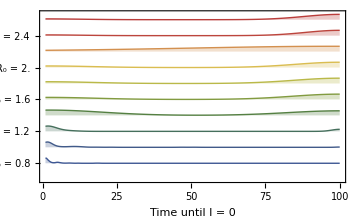

```mathematica
(* 1. RIDGE PLOT OF EXTINCTION-TIME DENSITIES BY R₀ ----------------------------- *)
(* expects: simulationResults :: <| 0.8 -> <|"ExtinctionTimes" -> {...}|>, ... |> *)

(* 1. pull data per r₀ --------------------------------------------------------- *)
r0Vals = SortBy[Keys[simulationResults], N];
extPerR0 = (simulationResults /@ r0Vals)[[All, "ExtinctionTimes"]];
dataByR0 = AssociationThread[r0Vals, extPerR0];
dataByR0 = Select[dataByR0, VectorQ[#, NumericQ] && Length[#] > 0 &];

(* 2. build kdes --------------------------------------------------------------- *)
bandwidth = Automatic;
dists = Map[SmoothKernelDistribution[#, bandwidth] &, dataByR0];

(* 3. compute common x-range and evaluation grid ------------------------------- *)
qMinMax = Map[Quantile[#, {0.01, 0.99}] &, Values[dataByR0]];
{xMin, xMax} = {Max[0, Min[qMinMax[[All, 1]]]], Max[qMinMax[[All, 2]]]};
xGrid = Subdivide[xMin, xMax, 300];

(* 4. set colors and ridge spacing -------------------------------------------- *)
r0Keys = Keys[dataByR0];
nGroups = Length[r0Keys];
colors = ColorData["DarkRainbow"] /@ Rescale[Range[nGroups]];
offset = 3;  (* vertical spacing between ridges *)

(* 5. build filled polygons, normalized to peak = 1 --------------------------- *)
ridgePolys =
  MapThread[
    Function[{r0, col},
      Module[{y = PDF[dists[r0], xGrid], yScale, yOff, poly, line},
        yScale = If[Max[y] > 0, y/Max[y], y];
        yOff = offset*(First@First@Position[r0Keys, r0] - 1);
        poly = Polygon@Join[Transpose[{xGrid, yScale}], {{Last[xGrid], 0}, {First[xGrid], 0}}];
        line = Line@Transpose[{xGrid, yScale}];

        {
          (* filled area with scoped style *)
          Style[Translate[poly, {0, yOff}],
            {FaceForm[Directive[col, Opacity[0.28]]], EdgeForm[None]}],
          (* outline with scoped style *)
          Style[Translate[line, {0, yOff}], Directive[col, Thick]]
        }
      ]
    ],
    {r0Keys, colors}
  ] // Flatten;

(* 6. y-axis ticks: one label per r₀ at each ridge baseline ------------------- *)
yTicks = Table[{offset*(i - 1), Row[{"R₀ = ", r0Keys[[i]]}]}, {i, nGroups}];

plot = Graphics[
  ridgePolys,
  Frame -> True,
  FrameLabel -> {Style["Time until I = 0", 14], Style["", 16], Style["", 16], Style["", 16]},
  FrameTicks -> {{yTicks, None}, {Automatic, None}},
  PlotRange -> {{xMin, xMax}, {-offset, offset*(nGroups - 1) + 1.05}},
  ImagePadding -> {{50, 10}, {40, 10}},  (* add a bit more bottom space *)
  AspectRatio -> 0.6,
  ImageSize -> Medium,
  FrameStyle -> Directive[Black, 12]  (* axis tick labels *)
];

Print[plot];
Export[FileNameJoin[{figsDir, "extinction-time-vs-r0-ridge.pdf"}], plot, "PDF"];
```

#### 2) the mean extinction time per R0

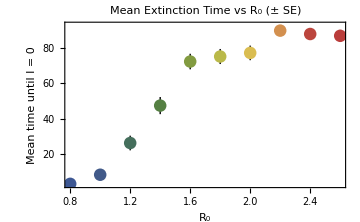

```mathematica
(* 5. MEAN EXTINCTION TIME VS R₀ (colored points, black error bars) ----------- *)
Module[
  {rVals, n, colors, numReps, means, sds, ses, basePoints, errorBars, pointPrims, plot},

  (* order r₀ exactly as in the ridge plot *)
  rVals = SortBy[r0Values, N];
  numReps = 100;

  (* compute summary stats *)
  means = Mean /@ (simulationResults[#]["ExtinctionTimes"] & /@ rVals);
  sds = StandardDeviation /@ (simulationResults[#]["ExtinctionTimes"] & /@ rVals);
  ses = sds / Sqrt[numReps];

  basePoints = Transpose[{rVals, means}];

  (* assign colors consistently with ridge plot *)
  n = Length[rVals];
  colors = ColorData["DarkRainbow"] /@ Rescale[Range[n]];

  (* draw vertical error bars (black) *)
  errorBars = Table[
    {Black, Line[{{rVals[[i]], means[[i]] - ses[[i]]}, {rVals[[i]], means[[i]] + ses[[i]]}}]},
    {i, n}
  ];

  (* color the points via epilog so bars stay black *)
  pointPrims = MapThread[
    {#2, PointSize[0.025], Point[#1]} &,
    {basePoints, colors}
  ];

plot = Show[
  ListPlot[
    basePoints,
    PlotStyle -> None,
    PlotMarkers -> None,
    Frame -> True,
    FrameLabel -> {
      Style["R₀", 16], 
      Style["Mean time until I = 0", 16]
    },
    PlotLabel -> Style["Mean Extinction Time vs R₀ (± SE)", 14],
    Epilog -> pointPrims,
    ImageSize -> Medium,
    FrameStyle -> Directive[Black, 12],  (* axis tick labels *)
    BaseStyle -> {FontSize -> 12}        (* overall text size fallback *)
  ],
  Graphics[errorBars],
  PlotRange -> All
];

  Print[plot];
  Export[FileNameJoin[{figsDir, "mean-extinction-time-vs-r0.pdf"}], plot, "PDF"];
]
```

## Look at how many sims out of n go to I=0 at t=1.

### In theory this will tell us how “fragile” the system is out of the gate

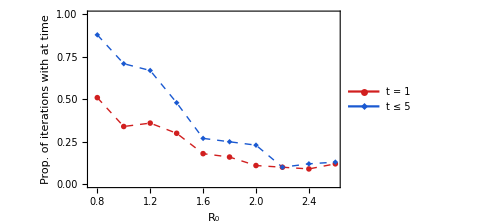

```mathematica
(* 1. PULL EXTINCTION TIMES BY R₀ ----------------------------------------------- *)

r0Vals = SortBy[Keys[simulationResults], N];

extByR0 = AssociationThread[
  r0Vals,
  (simulationResults /@ r0Vals)[[All, "ExtinctionTimes"]]
];

extByR0 = Select[extByR0, VectorQ[#, NumericQ] && Length[#] > 0 &];

(* 2. COUNT AT t = 1 AND AT/BEFORE t = 5 FOR EACH R₀ ---------------------------- *)

countsT1 = Count[#, 1] & /@ extByR0;
countsLe5 = Count[#, _?(# <= 5 &)] & /@ extByR0;
propsT1 = N[Lookup[countsT1, r0Vals]]/numReps;
propsLe5 = N[Lookup[countsLe5, r0Vals]]/numReps;

(* 3. BUILD {R₀, COUNT} POINTS IN KEY ORDER ------------------------------------ *)

pointsT1 = Transpose[{r0Vals, propsT1}];
pointsLe5 = Transpose[{r0Vals, propsLe5}];

(* 4. PLOT BOTH SERIES TOGETHER, DASHED LINES, DIFFERENT COLORS ----------------- *)

plot = ListLinePlot[
  {pointsT1, pointsLe5},
  Frame -> True,
  FrameLabel -> {Style["R₀", 14], Style["Prop. of iterations with  at time ", 13]},
  PlotMarkers -> {{●, 7}, {◆, 7}},
  PlotStyle -> {
    Directive[RGBColor[0.82, 0.12, 0.12], Dashed, Thick],   (* t = 1 *)
    Directive[RGBColor[0.10, 0.35, 0.82], Dashed, Thick]    (* t ≤ 5 *)
  },
  PlotLegends -> Placed[
    LineLegend[
      {RGBColor[0.82, 0.12, 0.12], RGBColor[0.10, 0.35, 0.82]},
      {"t = 1", "t ≤ 5"},
      LegendMarkerSize -> 14
    ],
    After
  ],
  PlotRange -> {All, {0, 1}},
  ImageSize -> Medium,
  FrameStyle -> Directive[Black, 12],  (* axis tick labels *)
  BaseStyle -> {FontSize -> 12} 
]

Export[FileNameJoin[{figsDir, 
	"proportion-of-extinctions-at-time-x-vs-r0.pdf"}],  plot,  "PDF"];
```

## Moving to weights given by an actual distribution

### We want to look what happens if we allow the weights to come from a uniform distribution something like then as q goes away from 0 towards 1/n then that means an increase in heterogeneity then in theory this increases the R0 on the landscape.

```mathematica
(* 2. FAST Q-SWEEP: R₀ VS WEIGHT HETEROGENEITY q -------------------------------- *)

SeedRandom[42];

(* 1. core parameters ---------------------------------------------------------- *)
r0 = 1.8;
numPatches = 2000000;
initialInfected = 1;

s = r0*numPatches;          (* machine real *)
sInt = Round[s];            (* exact integer *)

nt = sInt + initialInfected;

numReps = 100000;           (* make this big only after profiling *)
qValues = Range[0, 1/numPatches, 1/(5*numPatches)];

(* 2. helper: draw raw weights once, normalize to sum 1 ----------------------- *)
GeneratePatchWeights[q_] := Module[{raw},
  raw = RandomReal[{1/numPatches - q, 1/numPatches + q}, numPatches];
  raw/Total[raw]
];

(* 3. landscape-fixed, many replicates on the same weights -------------------- *)
SimulateR0FastSameWeights[q_, reps_] := Module[
  {weights, pickIdx, wSelected},
  weights = GeneratePatchWeights[q];
  (* draw indices of infected patches reps×, weighted by patch probabilities *)
  pickIdx = RandomChoice[weights -> Range[numPatches], reps];
  wSelected = weights[[pickIdx]];
  RandomVariate[BinomialDistribution[sInt, #]] & /@ wSelected
];

(* 4. fresh-weights each replicate: one binomial per run ---------------------- *)
SimulateR0FastFreshWeights[q_] := Module[
  {raw, total, infectedWeight},
  raw = RandomReal[{1/numPatches - q, 1/numPatches + q}, numPatches];
  total = Total[raw];
  infectedWeight = RandomChoice[raw -> (raw/total)];
  RandomVariate[BinomialDistribution[sInt, infectedWeight]]
];

(* 5. choose driver ------------------------------------------------------------ *)
ClearAll[SimulateR0Sample];
(* SimulateR0Sample[q_, reps_] := SimulateR0FastSameWeights[q, reps];  *)  (* preferred *)
SimulateR0Sample[q_, reps_] := Table[SimulateR0FastFreshWeights[q], {reps}];

(* 6. main q-sweep, timed ----------------------------------------------------- *)
LaunchKernels[];
numCores = $KernelCount;

Print["running q-sweep on ", numCores, " kernels …"];
t0 = AbsoluteTime[];

r0ComparisonResults = Association[];

Do[
  Module[{simVals, simMean, theoryR0},
    Print["  q = ", NumberForm[q, {3, 5}], " …"];
    simVals = SimulateR0FastSameWeights[q, numReps];
    simVals = Flatten[simVals];
    simMean = Mean[simVals];
    theoryR0 = (s/numPatches) + numPatches*s*(q^2/3.);
    r0ComparisonResults[q] = <|
      "SimulatedR0" -> simMean,
      "TheoreticalR0" -> theoryR0,
      "FirstStepInfections" -> simVals
    |>;
  ],
  {q, qValues}
];

dt = AbsoluteTime[] - t0;
Print[
  "finished in ", NumberForm[dt, {7, 1}], " s  |  ",
  "numReps = ", numReps, ", numPatches = ", numPatches,
  ", parallel kernels = ", numCores
];

Export[
  FileNameJoin[{NotebookDirectory[], "..", "..", "outputs", "intermediate-obs", "qVarSimResults_fast.wl"}],
  r0ComparisonResults
];
```

LaunchKernels::nodef: Some parallel subkernels are already running. Not launching default kernels again.

running q-sweep on 12 kernels …

q = 0 …

q = 1/10000000 …

q = 1/5000000 …

q = 3/10000000 …

q = 1/2500000 …

q = 1/2000000 …

finished in 6.4 s  |  numReps = 100000, numPatches = 2000000, parallel kernels = 12

```mathematica
(* read in instead of re-running *)
If[
  !ValueQ[r0ComparisonResults], 
  r0ComparisonResults = Import[
    FileNameJoin[
      {NotebookDirectory[], "..", "..", "outputs", "intermediate-obs", "qVarSimResults.wl"}
    ]
  ]
]
```

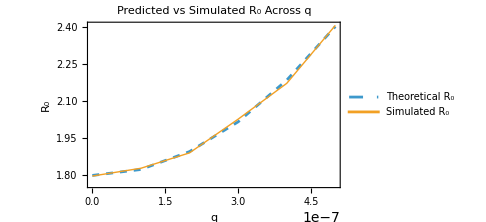

```mathematica
(* 1. PLOT: THEORETICAL VS SIMULATED R₀ (FIXED) -------------------------------- *)

Module[
  {qs, simVals, theoryVals, plot},

  (* 1. get the sorted q values ------------------------------------------------ *)
  qs = Sort[Keys[r0ComparisonResults]];

  (* 2. extract numeric fields from each inner association -------------------- *)
  simVals = (r0ComparisonResults[#]["SimulatedR0"] &) /@ qs;
  theoryVals = (r0ComparisonResults[#]["TheoreticalR0"] &) /@ qs;

  (* 3. build the two curves: theoretical then simulated ---------------------- *)
  plot = ListLinePlot[
    {Transpose[{qs, theoryVals}], Transpose[{qs, simVals}]},
    PlotStyle -> {{Dashed}, {Thick, Automatic}},
    PlotMarkers -> {None, Automatic},
    PlotLegends -> {"Theoretical R₀", "Simulated R₀"},
    Frame -> True,
    FrameLabel -> {Style["q", 14], Style["R₀", 14]},
    PlotLabel -> "",
    ImageSize -> Medium,
    FrameStyle -> Directive[Black, 12],  (* axis tick labels *)
    BaseStyle -> {FontSize -> 12} 
  ];

  Print[plot];
  Export[FileNameJoin[{figsDir, "predicted-vs-simulated-r0-with-q.pdf"}], plot, "PDF"];
];
```

```mathematica
r0ComparisonResults;
```

```mathematica
qs = Keys[r0ComparisonResults];  (* use actual keys *)

simVals = Association[
  Table[q -> r0ComparisonResults[q]["SimulatedR0"], {q, qs}]
];

seVals = Association[
  Table[
    q -> StandardDeviation[r0ComparisonResults[q]["FirstStepInfections"]] / 
           Sqrt[Length[r0ComparisonResults[q]["FirstStepInfections"]]],
    {q, qs}
  ]
]
```

<|0→(√(1438091/55555))/1200,1/10000000→(√(62275493/33333))/10000,1/5000000→(√(5100914791/11111))/150000,3/10000000→(√(5902657079/11111))/150000,1/2500000→(√(423155929/11111))/37500,1/2000000→(√(7810882879/11111))/150000|>

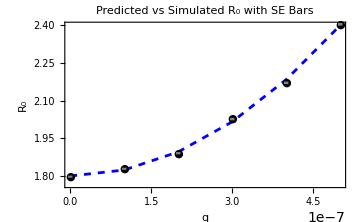

```mathematica
Module[
  {points, errorBars, meanList, seList, theoryVals, theoryLine},

  (* prepare mean and SE values *)
  points = Transpose[{qs, Values[simVals]}];
  meanList = Values[simVals];
  seList = Values[seVals];

  (* generate error bars manually using SE *)
  errorBars = Table[
    {
      Thickness[0.009],
      Gray,
      Line[{
        {qs[[i]], meanList[[i]] - seList[[i]]},
        {qs[[i]], meanList[[i]] + seList[[i]]}
      }]
    },
    {i, Length[qs]}
  ];

  (* compute theoretical R₀ values *)
  theoryVals = (S/numPatches + numPatches*S*(#^2/3) &) /@ qs;
  theoryLine = Transpose[{qs, theoryVals}];

  (* plot objects *)
  theoryPlot = ListLinePlot[
    theoryLine,
    PlotStyle -> {Dashed, Blue}
  ];

  simPlot = ListPlot[
    points,
    PlotStyle -> Black,
    PlotMarkers -> "●"
  ];

  (* final combined plot *)
  plotPointV = Show[
    theoryPlot,
    simPlot,
    Graphics[errorBars],
    Frame -> True,
    FrameLabel -> {"q", "R₀"},
    PlotLabel -> "Predicted vs Simulated R₀ with SE Bars",
    PlotLegends -> LineLegend[
      {"Theoretical R₀", "Simulated R₀ ± SE"},
      LegendMarkerSize -> 20
    ],
    ImageSize -> Medium
  ];
  Export[FileNameJoin[{figsDir, "predicted-vs-simulated-r0-with-q-points.pdf"}],  plotPointV,  "PDF"]; 
  plotPointV
]
```

Running UNIQUE-PATCH sims for R₀ = 0.8 (Nt = 160001)…

Running UNIQUE-PATCH sims for R₀ = 1. (Nt = 200001)…

Running UNIQUE-PATCH sims for R₀ = 1.2 (Nt = 240001)…

Running UNIQUE-PATCH sims for R₀ = 1.4 (Nt = 280001)…

Running UNIQUE-PATCH sims for R₀ = 1.6 (Nt = 320001)…

Running UNIQUE-PATCH sims for R₀ = 1.8 (Nt = 360001)…

Running UNIQUE-PATCH sims for R₀ = 2. (Nt = 400001)…

Running UNIQUE-PATCH sims for R₀ = 2.2 (Nt = 440001)…

Running UNIQUE-PATCH sims for R₀ = 2.4 (Nt = 480001)…

Running UNIQUE-PATCH sims for R₀ = 2.6 (Nt = 520001)…

/Users/colebrookson/github/theRmal-landscape/src/mathematica/../../outputs/intermediate-obs/simResults_unique.wl

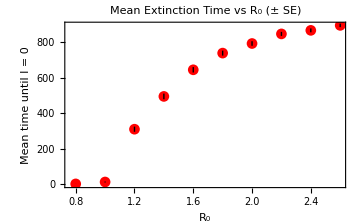

```mathematica
(* :::::::::::::::::::::::::::::::::::  FAST UNIQUE-PATCH VERSION  ::::::::::::::::::::::::::::::::::: *)
(* 
   assumptions in this stripped-down simulator
   -------------------------------------------------------------
   1. patches are chosen independently with replacement and all
      have equal probability (uniform weights).
   2. an infected individual survives exactly one step, so it
      never matters *which* patch holds how many infecteds –
      only how many *distinct* patches are occupied in a step. 
   3. susceptibles become infected if they land in any currently
      occupied patch; probability = (# infected patches) / P.
   4. we do *not* keep a record of which patch ids were used,
      only the count of unique ids each step.  this sacrifices
      any later spatial analysis that needs explicit ids, but
      buys a huge speed-up (no sparse arrays, no million-cell
      lists, no heavy bookkeeping).
   5. all downstream summaries (extinction time, epidemic size,
      etc.) are identical in format to  original code so the
      rest of pipeline works unchanged.
*)

(* 1.  fast per-run simulator using only unique-patch counts *)
ClearAll[simulateRunUnique]
maxTimeUnique = 1000;
numRepsUnique = 1000;

simulateRunUnique[totalIndividuals_] := Module[
  {t = 0, IT = initialInfected, NT = totalIndividuals,
   history = {},                     (* record infecteds through time *)
   patchSample, numInfPatches, sus, p, newInf, P = numPatches},
  
  While[IT > 0 && t < maxTimeUnique,
    
    (* drop current infecteds onto patches *)
    patchSample   = RandomInteger[{1, P}, IT];
    numInfPatches = Length@DeleteDuplicates[patchSample];
    
    (* draw new infections among susceptibles *)
    sus   = NT - IT;
    p     = N[numInfPatches]/P;      (* share-a-patch probability *)
    newInf = If[sus <= 0, 0,
                RandomVariate[BinomialDistribution[sus, p]]];
    
    AppendTo[history, IT];
    IT = newInf;
    t++
  ];
  
  <|
    "ExtinctionTime"         -> t,
    "InfectedTimeSeries"     -> history,
    "MaxProportionInfected"  -> Max[history]/totalIndividuals,
    "EpidemicSize"           -> Total[history],
    "DurationAboveThreshold" -> Count[history, x_ /; x > threshold]
  |>
]

(*
  ok so we don't actually care which exact patches get hit, only
  whether a susceptible ends up sharing any patch with an infect-ed.

  reasoning:
    • there are p = numPatches identical sites, each chosen with prob 1/p
    • each infected “tags” its own patch ⇒ prob a given patch stays clean
      after it picks is (1-1/p)
    • with it infecteds the chance a *specific* patch is still clean is
          (1-1/p)^it
    • flip viewpoint: for one susceptible the chance it lands on at
      least one tagged patch is
          p_t = 1 - (1-1/p)^it
    • when p is big this is ≈ 1  exp(-it/p)  (handy if you want a float)

  bottom line: we can skip drawing millions of patch labels; just draw
  new infections ~ Binomial[nt-it,  p_t].
*)
ClearAll[simulateRunFast]
simulateRunFast[totalIndividuals_, horizon_: maxTimeUnique] :=
 Module[{t = 0, IT = initialInfected, NT = totalIndividuals,
         history = {}, P = numPatches, p, newInf},
  
  While[IT > 0 && t < horizon,
    p      = 1. - (1. - 1./P)^IT;              (* O(1) *)
    newInf = RandomVariate[BinomialDistribution[NT - IT, p]];
    AppendTo[history, IT];
    IT = newInf; t++];
  
  <|
    "ExtinctionTime"         -> t,
    "InfectedTimeSeries"     -> history,
    "MaxProportionInfected"  -> Max[history]/totalIndividuals,
    "EpidemicSize"           -> Total[history],
    "DurationAboveThreshold" -> Count[history, x_ /; x > threshold]
  |>
]

(* 2.  main simulation loop — identical structure, just swaps in the new function *)
uniqueSimulationResults = Association[];

Do[
  Module[
    {Nt = Round[r0*numPatches + initialInfected],
     counter = 0, results, extinctionTimes, timeSeriesList,
     propMax, sizes, durations, maxLen, aligned, meanOverTime, varOverTime},
    
    Print["Running UNIQUE-PATCH sims for R₀ = ", r0, " (Nt = ", Nt, ")…"];
    SetSharedVariable[counter];
    
    results = Monitor[
      ParallelTable[
        Module[{out = simulateRunFast[Nt]},
          counter++; out],
        {numRepsUnique}
      ],
      Row[{
        "Progress: ", counter, "/", numRepsUnique, " (",
        Round[100.0*counter/numRepsUnique], "%)"
      }]
    ];
    
    extinctionTimes = results[[All, "ExtinctionTime"]];
    timeSeriesList  = results[[All, "InfectedTimeSeries"]];
    propMax         = results[[All, "MaxProportionInfected"]];
    sizes           = results[[All, "EpidemicSize"]];
    durations       = results[[All, "DurationAboveThreshold"]];
    
    maxLen   = Min[maxTimeUnique, Max[Length /@ timeSeriesList]];
    aligned  = Transpose[PadRight[#, maxLen, 0] & /@ timeSeriesList];
    meanOverTime = Mean /@ aligned;
    varOverTime  = Variance /@ aligned;
    
    uniqueSimulationResults[r0] = <|
      "ExtinctionTimes"           -> extinctionTimes,
      "MeanInfectedOverTime"      -> meanOverTime,
      "InfectedTimeSeries"        -> timeSeriesList,
      "VarianceInfectedOverTime"  -> varOverTime,
      "MaxProportionInfected"     -> propMax,
      "EpidemicSizes"             -> sizes,
      "DurationsAboveThreshold"   -> durations,
      "ExtinctionProbability"     -> Count[extinctionTimes, t_ /; t < maxTimeUnique]/numRepsUnique
    |>;
  ],
  {r0, r0Values}
];

(* 3.  export results to the same outputs folder with a distinct filename *)
Export[
  FileNameJoin[
    {NotebookDirectory[], "..", "..", "outputs", "intermediate-obs", "simResults_unique.wl"}
  ],
  uniqueSimulationResults
]

(* 5. MEAN EXTINCTION TIME VS R₀ (with error bars drawn manually) ------------ *)

Module[
  {rVals, means, sds, ses, basePoints, errorBars, plot, numReps},

  rVals = r0Values;
  numReps = numRepsUnique; (* adjust to whatever was used during simulations *)

  (* compute mean and SD of extinction times per R₀ *)
  means = Mean /@ (uniqueSimulationResults[#]["ExtinctionTimes"] & /@ rVals);
  sds = StandardDeviation /@ (uniqueSimulationResults[#]["ExtinctionTimes"] & /@ rVals);

  (* compute standard error = SD / sqrt(n) *)
  ses = sds / Sqrt[numReps];

  basePoints = Transpose[{rVals, means}];

  (* draw vertical error bars for ±SE *)
  errorBars = Table[
    {
      Black,
      Line[{{rVals[[i]], means[[i]] - ses[[i]]}, {rVals[[i]], means[[i]] + ses[[i]]}}]
    },
    {i, Length[rVals]}
  ];

  plot = Show[
    ListPlot[
      basePoints,
      PlotStyle -> Red,
      PlotMarkers -> Automatic,
      Frame -> True,
      FrameLabel -> {"R₀", "Mean time until I = 0"},
      PlotLabel -> "Mean Extinction Time vs R₀ (± SE)",
      ImageSize -> Medium
    ],
    Graphics[errorBars]
  ];

  Print[plot];
]
```